Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

A few problems refer to example 1, p. 985, where a spanning tree for the following graph is discussed.

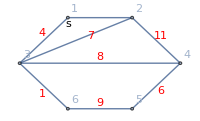

```mathematica
example1graph=Graph[{1<->2,2<->4,4<->5,5<->6,6<->3,3<->1,3<->2,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{2,0},{3.5,-1.5},{2,-3},{0,-3},{-1.5,-1.5}},EdgeWeight->{2,11,6,9,1,4,7,8},Epilog->{{Text[Style["s",Medium],{0,-0.2}]},{Red,Text[Style["6",Medium],{2.9,-2.4}]},{Red,Text[Style["1",Medium],{-0.8,-2.5}]},{Red,Text[Style["4",Medium],{-0.8,-0.5}]},{Red,Text[Style["8",Medium],{1,-1.3}]},{Red,Text[Style["9",Medium],{1,-2.8}]},{Red,Text[Style["7",Medium],{0.7,-0.6}]},{Red,Text[Style["2",Medium],{1,0.2}]},{Red,Text[Style["11",Medium],{2.9,-0.6}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
FindSpanningTree[example1graph];
HighlightGraph[example1graph,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[example1graph]]
```

21.

1 - 6 Kruskal’s greedy algorithm
Find a shortest spanning tree by Kruskal’s algorithm. Sketch it.

1. Problem represented by a diagram.

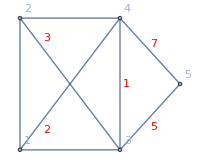

```mathematica
g5=Graph[{1<->2,2<->3,3<->4,4<->5,3<->5,2<->4,1<->4,1<->3},VertexLabels->"Name",VertexCoordinates->{{0,0},{0,2},{1.5,0},{1.5,2},{2.4,1}},EdgeWeight->{8,3,1,7,5,2,2,4},Epilog->{{Text[Style["s",Medium],{0,-0.15}]},{Red,Text[Style["8",Medium],{-0.12,1}]},{Red,Text[Style["1",Medium],{1.6,1}]},{Red,Text[Style["4",Medium],{0.7,-0.15}]},{Red,Text[Style["2",Medium],{0.8,2.12}]},{Red,Text[Style["3",Medium],{0.4,1.7}]},{Red,Text[Style["7",Medium],{2,1.6}]},{Red,Text[Style["2",Medium],{0.4,0.3}]},{Red,Text[Style["5",Medium],{2,0.35}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
FindSpanningTree[g5];
HighlightGraph[g5,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g5]]
```

10.

The highlighted graph and green cell above match the answer in the text.

3.  Problem represented by a diagram.

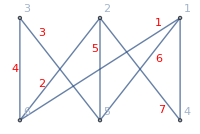

```mathematica
g6=Graph[{1<->4,4<->2,2<->5,5<->3,3<->6,1<->5,1<->6,2<->6},VertexLabels->"Name",VertexCoordinates->{{0,0},{0,-2},{-1.5,0},{-1.5,-2},{-3,0},{-3,-2}},EdgeWeight->{8,7,5,3,4,6,1,2},Epilog->{{Text[Style["s",Medium],{0,0.15}]},{Red,Text[Style["4",Medium],{-3.1,-1}]},{Red,Text[Style["3",Medium],{-2.6,-0.3}]},{Red,Text[Style["2",Medium],{-2.6,-1.3}]},{Red,Text[Style["5",Medium],{-1.6,-0.6}]},{Red,Text[Style["1",Medium],{-0.4,-0.1}]},{Red,Text[Style["7",Medium],{-0.35,-1.8}]},{Red,Text[Style["6",Medium],{-0.4,-0.8}]},{Red,Text[Style["8",Medium],{0.14,-1}]}},ImageSize->200,ImagePadding->10]
```

```mathematica
FindSpanningTree[g6];
HighlightGraph[g6,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g6]]
```

17.

The highlighted graph and the green cell above match the answer in the text.

5.  Problem represented by a diagram.

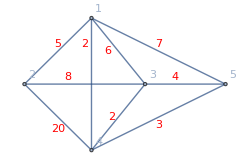

```mathematica
g7=Graph[{1<->2,1<->4,1<->3,1<->5,2<->3,3<->5,2<->4,4<->5,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{-2,-2},{0,-4},{1.6,-2},{4,-2}},EdgeWeight->{5,2,6,7,8,4,20,3,2},Epilog->{{Text[Style["s",Medium],{0,0.25}]},{Red,Text[Style["5",Medium],{-1,-0.8}]},{Red,Text[Style["20",Medium],{-1,-3.35}]},{Red,Text[Style["8",Medium],{-0.7,-1.8}]},{Red,Text[Style["3",Medium],{2,-3.25}]},{Red,Text[Style["7",Medium],{2,-0.8}]},{Red,Text[Style["2",Medium],{0.6,-3}]},{Red,Text[Style["2",Medium],{-0.2,-0.8}]},{Red,Text[Style["6",Medium],{0.5,-1}]},{Red,Text[Style["4",Medium],{2.5,-1.8}]}},ImageSize->250,ImagePadding->10]
```

```mathematica
FindSpanningTree[g7];
HighlightGraph[g7,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[g7]]
```

12.

The highlighted graph and the green cell above match the answer in the text.

8.  To get a minimum spanning tree, instead of adding shortest edges, one could think of deleting longest edges. For what graphs would this be feasible? Describe an algorithm for this.

9.  Apply the method suggested in problem 8 to the graph in example 1. Do you get the same tree?

I’m only a button pusher right now.

10.  Design an algorithm for obtaining longest spanning trees.

11. Apply the algorithm in problem 10 to the graph in example 1. Compare with the result in example 1.

The documentation led me to think the following would work. It does not seem to work. It gives edges which are in disagreement with the text answer, and the total is 29, not 38, as the text maintains.

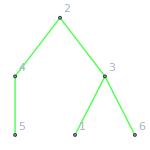

```mathematica
g9=FindSpanningTree[example1graph,EdgeWeight->-1,ImageSize->150,EdgeStyle->Green,VertexLabels->"Name"]
```

Below I rename the graph and reverse the sign on all the edge weights by hand.

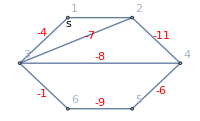

```mathematica
ex2=Graph[{1<->2,2<->4,4<->5,5<->6,6<->3,3<->1,3<->2,3<->4},VertexLabels->"Name",VertexCoordinates->{{0,0},{2,0},{3.5,-1.5},{2,-3},{0,-3},{-1.5,-1.5}},EdgeWeight->{-2,-11,-6,-9,-1,-4,-7,-8},Epilog->{{Text[Style["s",Medium],{0,-0.2}]},{Red,Text[Style["-6",Medium],{2.9,-2.4}]},{Red,Text[Style["-1",Medium],{-0.8,-2.5}]},{Red,Text[Style["-4",Medium],{-0.8,-0.5}]},{Red,Text[Style["-8",Medium],{1,-1.3}]},{Red,Text[Style["-9",Medium],{1,-2.8}]},{Red,Text[Style["-7",Medium],{0.7,-0.6}]},{Red,Text[Style["-2",Medium],{1,0.2}]},{Red,Text[Style["-11",Medium],{2.9,-0.6}]}},ImageSize->200,ImagePadding->10]
```

Then I run FindSpanningTree, and see that the correct edges are picked.

```mathematica
FindSpanningTree[ex2];
HighlightGraph[ex2,%,GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[ex2]]
```

-38.

And, except for an expected sign reversal, the correct integer sum is returned.

13.  Air cargo. Find a shortest spanning tree in the complete graph of all possible 15 connections between the six cities given (distances by airplane, in miles, rounded). Can you think of a practical application of the result?

```mathematica
Grid[{{"","Dallas_2","Denver_3","Los Angeles_4","New York_5","Washington,D.C_6"},{"Chicago_1",800,900,1800,700,650},{"Dallas","",650,1300,1350,1200},{"Denver","","",850,1650,1500},{"Los Angeles","","","",2500,2350},{"New York","","","","",200}},Frame->All]
```

| Dallas_2 | Denver_3 | Los Angeles_4 | New York_5 | Washington,D.C_6
Chicago_1 | 800 | 900 | 1800 | 700 | 650
Dallas |  | 650 | 1300 | 1350 | 1200
Denver |  |  | 850 | 1650 | 1500
Los Angeles |  |  |  | 2500 | 2350
New York |  |  |  |  | 200

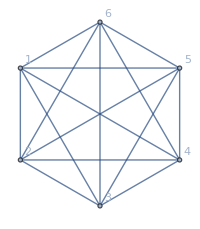

```mathematica
cg=Graph[{1<->2,2<->3,3<->4,4<->5,5<->6,6<->1,1<->4,1<->5,3<->5,3<->6,4<->6,4<->2,5<->2,6<->2,1<->3},EdgeWeight->{800,650,850,2500,200,650,1800,700,1650,1500,2350,1300,1350,1200,900},GraphLayout->"CircularEmbedding",VertexLabels->"Name",ImageSize->200]
```

```mathematica
FindSpanningTree[cg];
HighlightGraph[cg,%,GraphHighlightStyle->"Thick",ImagePadding->10]
```

-Graphics-

The spanning tree presented above agrees with the text answer, i.e. 5-6-1-2-3-4 would make the shortest continuous sequence of flights. The text answer does not report the distance, which is 3600, as shown below.

```mathematica
size[g_]:=With[{edges=EdgeList[FindSpanningTree[{g,1}]]},Total[PropertyValue[{g,#},EdgeWeight]&/@edges]]
N[size[cg]]
```

3600.

From the data given, it happens that the shortest distance is not always a straight line. An airline scheduler might want to look at the following grid, to see if it might shorten the overall trip.

```mathematica
Grid[Table[FindShortestPath[cg,m,n,Method->"Dijkstra"],{n,1,6},{m,1,6}],Frame->All]
```

{1} | {2,1} | {3,1} | {4,3,1} | {5,1} | {6,1}
{1,2} | {2} | {3,2} | {4,2} | {5,2} | {6,2}
{1,3} | {2,3} | {3} | {4,3} | {5,1,3} | {6,3}
{1,3,4} | {2,4} | {3,4} | {4} | {5,1,3,4} | {6,4}
{1,5} | {2,5} | {3,1,5} | {4,3,1,5} | {5} | {6,5}
{1,6} | {2,6} | {3,6} | {4,6} | {5,6} | {6}

Or something like the following could also be considered, which essentially creates a new graph for each new situation.

```mathematica
c1=GeoPosition[Entity["City",{"Chicago","Illinois","UnitedStates"}]];
c2=GeoPosition[Entity["City",{"Dallas","Texas","UnitedStates"}]];
c3=GeoPosition[Entity["City",{"Denver","Colorado","UnitedStates"}]];
c4=GeoPosition[Entity["City",{"LosAngeles","California","UnitedStates"}]];
c5=GeoPosition[Entity["City",{"NewYork","NewYork","UnitedStates"}]];
c6=GeoPosition[Entity["City",{"Washington","DistrictOfColumbia","UnitedStates"}]];
```

An example itinerary.

```mathematica
FindShortestTour[{c1,c2,c3}]
```

{3.8139×10^6 m,{1,3,2,1}}

14 - 20 General properties of trees
Prove the following. Hint. Use problem 14 in proving 15 and 18; use problems 16 and 18 in proving 20.

15.  If in a graph any two vertices are connected by a unique path, the graph is a tree.

19.  If two vertices in a tree are joined by a new edge, a cycle is formed.